```mathematica
α1=0.1;
α2=0;
α3=-0.2;
β=0.1;
```

```mathematica
(*free energy*)(*Field zero*)eq1=α1(psi[x,y,z]^2)+1/2 β(psi[x,y,z]^4);(*Alpha positivo*)eq2=α2(psi[x,y,z]^2)+1/2 β(psi[x,y,z]^4);(*Alpha nulo*)eq3=α3(psi[x,y,z]^2)+1/2 β(psi[x,y,z]^4);(*Alpha negativo*)
```

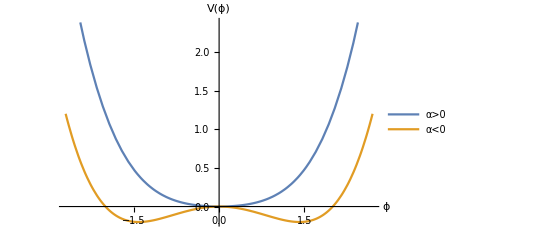

```mathematica
Plot[{eq1,eq3},{psi[x,y,z],-2.7,2.7},AxesLabel -> {"ϕ","V(ϕ)"}, PlotLegends -> {"α>0","α<0"}]
```